```mathematica
FullSimplify[s^3+8 s^2+24 s+32]
```

(4+s) (8+s (4+s))

```mathematica
Roots[(s+3)^5==0,s]
```

s==-3||s==-3||s==-3||s==-3||s==-3

```mathematica
Apart[(s+3)^5]
```

243+405 s+270 s^2+90 s^3+15 s^4+s^5

```mathematica
Apart[(s^2+6 s+3)/(s+3)^5]
```

-6/(3+s)^5+1/(3+s)^3

```mathematica
Convolve[InverseLaplaceTransform[(R/L)/(s+R/L),s,t],Cos[ω t],t,y]
```

(R Convolve[ⅇ^(-(R t)/L),Cos[t ω],t,y])/L

```mathematica
InverseLaplaceTransform[(R/L)/(s+R/L)*s/(ω^2+s^2),s,t]
```

(ⅇ^(-(R t)/L) R (-R+ⅇ^((R t)/L) R Cos[t ω]+ⅇ^((R t)/L) L ω Sin[t ω]))/(R^2+L^2 ω^2)

```mathematica
Abs[(R/L)/(ⅉ ω+R/L)]
```

```mathematica
Re[R/(L (R/L+ⅈ ω))]
```

Re[R/(L (R/L+ⅈ ω))]

```mathematica
FullSimplify[R/(L (R/L+ⅈ ω))]
```

R/(R+ⅈ L ω)

```mathematica
Element[{R,L,ω},Reals]
```

(R|L|ω)∈ℝ

```mathematica
Re[R/(R+ⅈ L ω)]
```

Re[R/(R+ⅈ L ω)]

```mathematica
Collect[%,ⅉ]
```

```mathematica
R/(R+j L ω)*1/(R- j L ω)
```

```mathematica
R/((R-j L ω) (R+j L ω))//Expand
```

```mathematica
R/((R-j L ω) (R+j L ω))//FullSimplify
```

```mathematica
R/(R^2-j^2 L^2 ω^2)/.j^2-> -1
```

```mathematica
R/(R^2+L^2 ω^2)*(R-j L ω)
```

(R (R-j L ω))/(R^2+L^2 ω^2)

```mathematica
Collect[%,j]
```

R^2/(R^2+L^2 ω^2)-(j L R ω)/(R^2+L^2 ω^2)

```mathematica
(R^2/(R^2+L^2 ω^2))^2+((j L R ω)/(R^2+L^2 ω^2)*1/j)^2
```

R^4/((R^2+L^2 ω^2)^2)+(L^2 R^2 ω^2)/((R^2+L^2 ω^2)^2)

```mathematica
Sqrt[%]
```

√(R^4/((R^2+L^2 ω^2)^2)+(L^2 R^2 ω^2)/((R^2+L^2 ω^2)^2))

```mathematica
Simplify[√(R^4/((R^2+L^2 ω^2)^2)+(L^2 R^2 ω^2)/((R^2+L^2 ω^2)^2))]
```

√(R^2/(R^2+L^2 ω^2))

```mathematica
ArcTan[((- L R ω)/(R^2+L^2 ω^2))/(R^2/(R^2+L^2 ω^2))]
```

-ArcTan[(L ω)/R]

```mathematica
ArcTan[0]
```

0

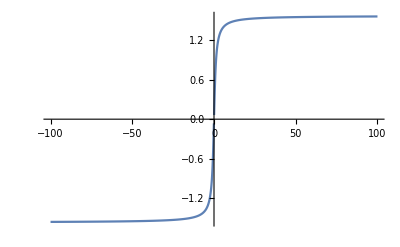

```mathematica
Plot[ArcTan[x],{x,-100,100}]
```